```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_],TSloshingMolin2018[B1_,B2_,L1_,L2_,draft_,depth_,max_:100],TPistonMolin2018[B1_,B2_,L1_,L2_,draft_,depth_,max_:100]}

```mathematica
h=1.36;
Column@Table[{T,2π/getkFromTandDepth[T,h]},{T,{0.87,1.22,1.57,1.91,2.26,2.61,3.31}}]
```

{0.87,1.18175}
{1.22,2.32091}
{1.57,3.76694}
{1.91,5.26816}
{2.26,6.7854}
{2.61,8.25369}
{3.31,11.0791}

```mathematica
import[filename_]:=Module[{lines,dataStart},
(*lines=Import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial01/time.txt","Lines"];*)
lines=Import[filename,"Lines"];
(*"% [Data]" の行番号を特定*)
dataStart=First@Flatten@Position[lines,"% [Data]"]+1;
(*データ部だけを取得して数値としてインポート*)
Return@ImportString[StringRiffle[lines[[dataStart;;]]],"Table"][[1]];
]
```

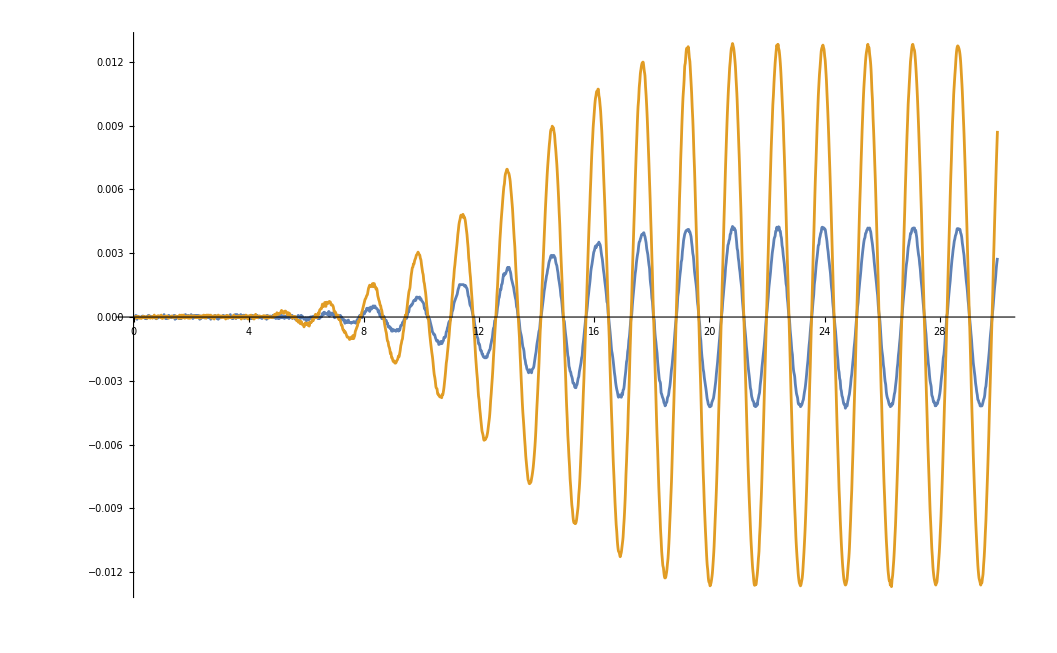

```mathematica
ListPlot[Table[Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial"<>no<>".csv","CSV"],{no,{(*"01","02","03","04","05","06",*)"07","08"(*,"09","10","11","12","13","14","15","16","17","18","19","20","21","22","23"*)}}],Joined->True,PlotRange->All]
```

```mathematica
n=2000;
Do[
trial="Trial"<>no;
(*データの読み込みと整形*)
dir="/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/data/WECSIM/inter/RegularWaveTuning1/"<>trial;
Print[(timeData=24*60*60 (import[dir<>"/time.txt"][[;;n]]-import[dir<>"/time.txt"][[1]]))[[;;10]]]
,{no,{"01","02","03","04","05","06","07","08","09","10","11","12","13","14","15","16","17","18","19","20","21","22","23"}}]
```

{0.,0.0200016,0.0400032,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.179997}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0800064,0.0999994,0.120001,0.140003,0.160004,0.180006}

{0.,0.019993,0.0399946,0.0599962,0.0799978,0.0999994,0.119992,0.139994,0.159996,0.179997}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.139994,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0800064,0.0999994,0.120001,0.140003,0.160004,0.180006}

{0.,0.0200016,0.0400032,0.0600048,0.0800064,0.0999994,0.120001,0.140003,0.160004,0.180006}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.139994,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.180006}

{0.,0.0200016,0.0400032,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.179997}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.179997}

{0.,0.019993,0.0399946,0.0599962,0.0799978,0.0999994,0.119992,0.139994,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.179997}

{0.,0.0200016,0.0400032,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.179997}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.139994,0.159996,0.179997}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0800064,0.0999994,0.120001,0.140003,0.160004,0.180006}

{0.,0.0200016,0.0399946,0.0599962,0.0799978,0.0999994,0.120001,0.140003,0.159996,0.179997}

{0.,0.0200016,0.0400032,0.0600048,0.0799978,0.0999994,0.120001,0.140003,0.160004,0.180006}

```mathematica
Do[
trial="Trial"<>no;(*データの読み込みと整形*)
dir="/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/data/WECSIM/inter/RegularWaveTuning1/"<>trial;
timeData=24*60*60 (import[dir<>"/time.txt"][[;;]]-import[dir<>"/time.txt"][[1]]);
dispData=import[dir<>"/wmdisp15.txt"][[;;]]-Mean@import[dir<>"/wmdisp15.txt"][[1;;100]];
data=Transpose[{timeData,dispData}];
f=Interpolation[data,InterpolationOrder->3];
csv=Table[{t,f[t]},{t,0,50.,0.01}];
PrependTo[csv,{-csv[[2,1]],csv[[1,2]]}];
Export[file=FileNameJoin[{NotebookDirectory[],trial<>".csv"}],csv,"CSV"];
Print[file];
,{no,{"01","02","03","04","05","06","07","08","09","10","11","12","13","14","15","16","17","18","19","20","21","22","23"}}]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial01.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial02.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial03.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial04.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial05.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial06.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial07.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial08.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial09.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial10.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial11.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial12.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial13.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial14.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial15.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial16.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial17.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial18.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial19.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial20.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial21.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial22.csv

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial23.csv

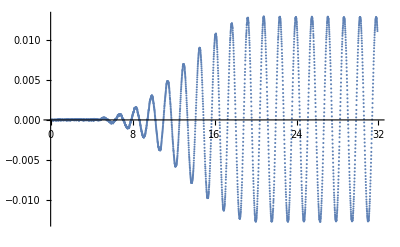

```mathematica
ListPlot[Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ruehl2016/Trial08.csv","CSV"]]
```

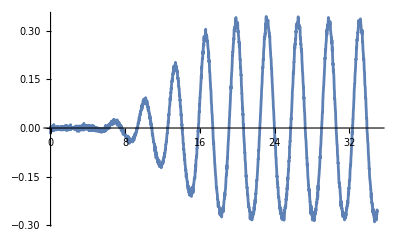

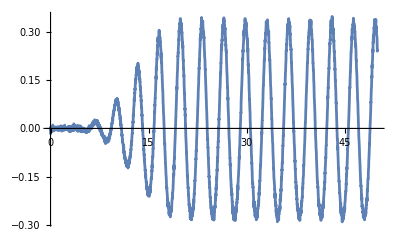

```mathematica
ListPlot[data,Joined->True]
data=Table[{X,f'[X]},{X,0,50,0.01}];
ListPlot[data,Joined->True]
```

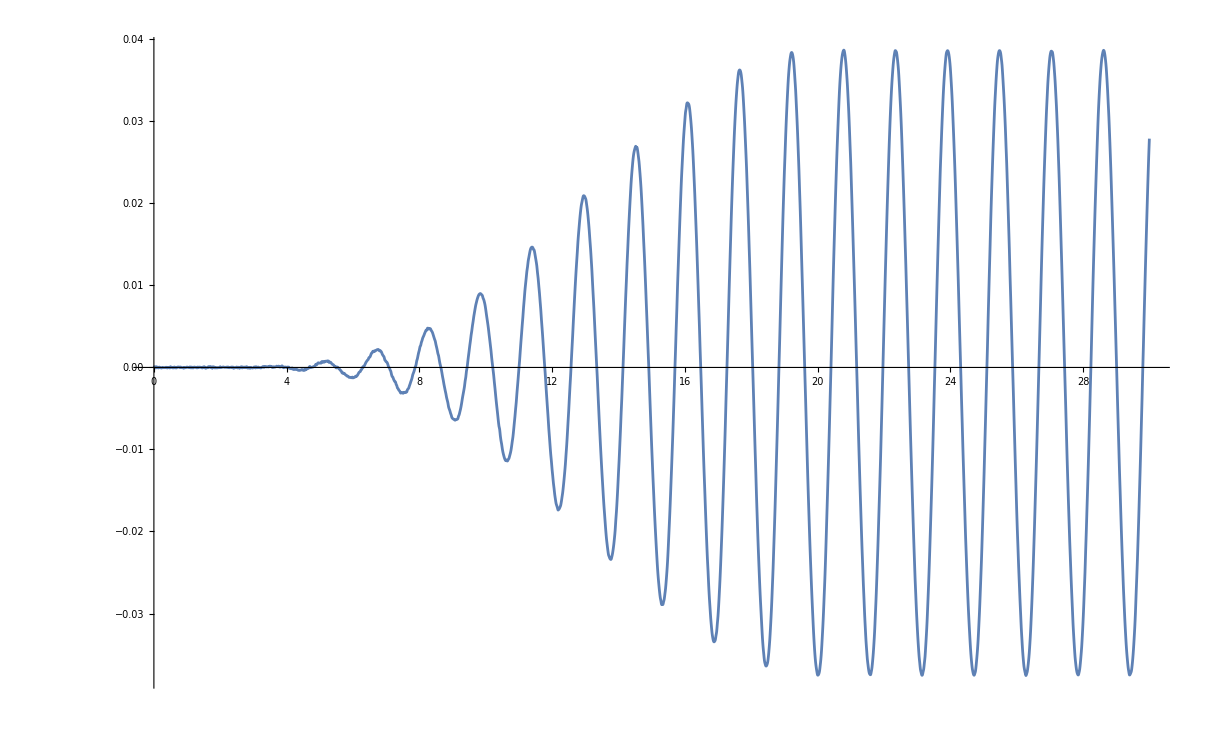

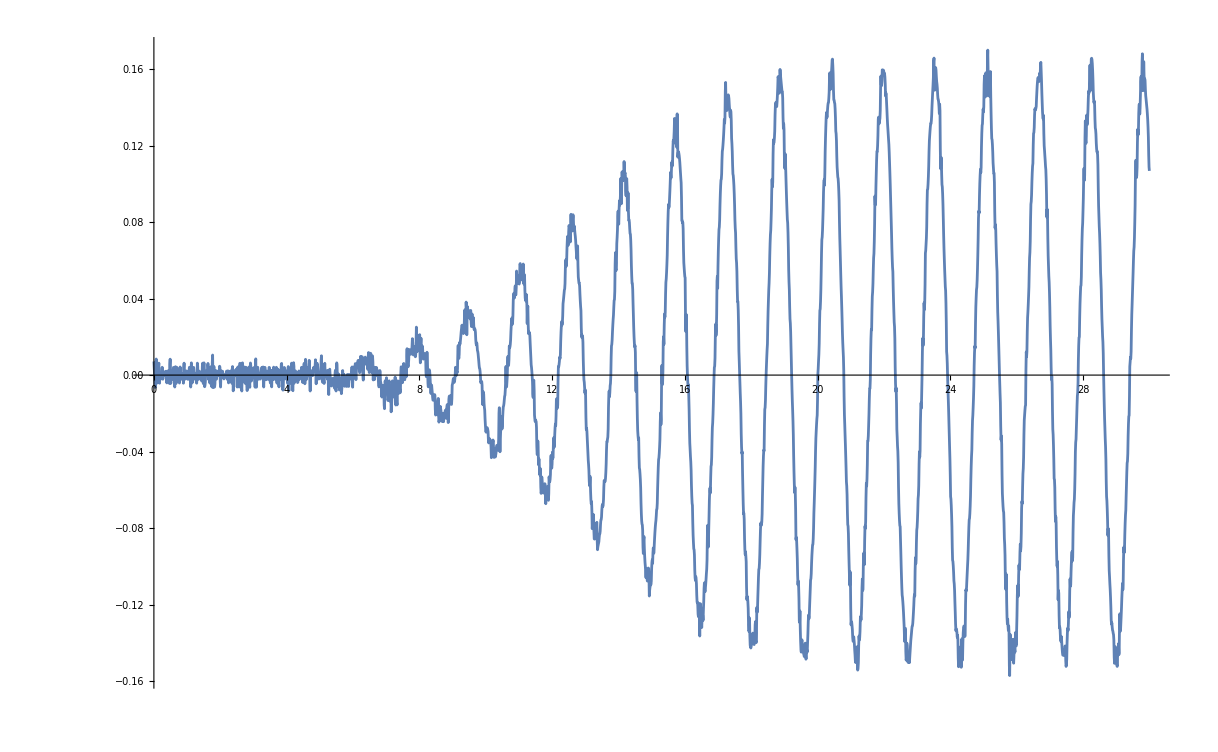

```mathematica
(*小数点10桁、指数なしで表示形式に変換*)
ListPlot[{X,Integrate[df[x],{x,0,X,0.001}]},{X,0,20,0.1}]
cppList=StringJoin["{",StringRiffle[Map[StringJoin["{",StringRiffle[Map[ToString[NumberForm[#,{Infinity,10},ExponentFunction->(Function[exp,Null])]]&,#],","],"}"]&,data],","],"}"];
(*Export["/Users/tomoaki/Downloads/data_for_cpp.txt",cppList,"Text"]*)
```

```mathematica
Export["/Users/tomoaki/Downloads/formatted_data.csv",csv,"Text"]
```

/Users/tomoaki/Downloads/formatted_data.csv

```mathematica
n=3000;
data=Transpose[{
24*60*60(import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txt"][[;;n]]-import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txt"][[1]]),
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/wmdisp15.txt"][[;;n]]}]
ListPlot[data]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の1から3000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/wmdisp15.txtが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

General::stop: この計算中に，First::nofirstのこれ以上の出力は表示されません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

General::stop: この計算中に，StringRiffle::listのこれ以上の出力は表示されません．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

General::stop: この計算中に，ImportString::stringのこれ以上の出力は表示されません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の1から3000の位置が取れません．

{86400 (-$Failed⟦1+First[{}];;All⟧+StringRiffle[$Failed⟦1+First[{}];;All⟧]⟦1;;3000⟧),StringRiffle[$Failed⟦1+First[{}];;All⟧]⟦1;;3000⟧}

-Graphics-

```mathematica
ListPlot[
Transpose[{
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txt"][[100;;5000]],
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/wmdisp15.txt"][[100;;5000]]}]
,Joined->True,AspectRatio->1/10,ImageSize->2000]

ListPlot[
Transpose[{
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/time.txt"][[100;;5000]],
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/wmdisp15.txt"][[100;;5000]]}]
,Joined->True,AspectRatio->1/10,ImageSize->2000]

ListPlot[
Table[Transpose[{
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txt"][[100;;5000]],
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/wg"<>ToString[i]<>".txt"][[100;;5000]]}],{i,{3,6}}]
,Joined->True,AspectRatio->1/10,ImageSize->2000]
ListPlot[
Table[Transpose[{
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/time.txt"][[100;;5000]],
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/wg"<>ToString[i]<>".txt"][[100;;5000]]}],{i,{3,6}}]
,Joined->True,AspectRatio->1/10,ImageSize->2000]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/wmdisp15.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/wmdisp15.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/wg3.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial13/time.txtが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

General::stop: この計算中に，First::nofirstのこれ以上の出力は表示されません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

General::stop: この計算中に，StringRiffle::listのこれ以上の出力は表示されません．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

General::stop: この計算中に，ImportString::stringのこれ以上の出力は表示されません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/wg3.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning2/Trial13/time.txtが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

General::stop: この計算中に，First::nofirstのこれ以上の出力は表示されません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

General::stop: この計算中に，StringRiffle::listのこれ以上の出力は表示されません．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

General::stop: この計算中に，ImportString::stringのこれ以上の出力は表示されません．

Part::take: StringRiffle[$Failed⟦1+First[{}];;All⟧]の100から5000の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

-Graphics-

```mathematica
Table[ListPlot[Transpose[{
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial0"<>ToString[i]<>"/time.txt"],
import["/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial0"<>ToString[i]<>"/wg1.txt"]}],Joined->True],{i,1,5}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial01/time.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial01/wg1.txtが見付かりませんでした．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

Import::nffil: Importの最中にファイル/Users/tomoaki/Downloads/310/FOSWEC/data/WECSIM/inter/RegularWaveTuning1/Trial02/time.txtが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

First::nofirst: {}の長さはゼロで最初の要素は存在しません．

General::stop: この計算中に，First::nofirstのこれ以上の出力は表示されません．

Part::span: 1+First[{}];;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

StringRiffle::list: StringRiffle[$Failed⟦1+First[{}];;All⟧]の位置1にはリストが想定されています．

General::stop: この計算中に，StringRiffle::listのこれ以上の出力は表示されません．

ImportString::string: 第1引数StringRiffle[$Failed⟦1+First[{}];;All⟧]は文字列ではありません．

General::stop: この計算中に，ImportString::stringのこれ以上の出力は表示されません．

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}